```mathematica
<<EcoEvo`
```

EcoEvo Package Version 0.9.2β (August 9, 2018)

## Logistic equation

Here we will explore the logistic equation dn/dt=rn(1-n/k)=f(n)

```mathematica
SetModel[{Pop[1]->{Variable->n,Equation:>f[n[t]]}}]
```

### Plot dn/dt vs n.

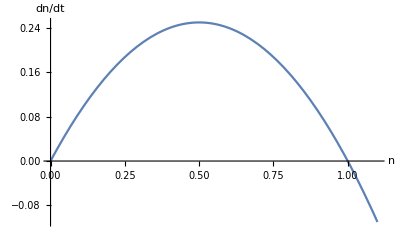

```mathematica
r=1.0;
k=1.0;

f[n_]:=r*n*(1-n/k);

Plot[f[n],{n,0,1.1},AxesLabel->{"n","dn/dt"}]
```

### Solve the model numerically for different initial conditions.

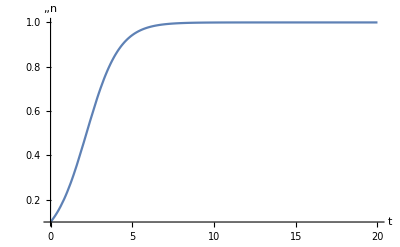

```mathematica
tmax=20;
sol=EcoSim[{n->0.1},tmax];
PlotDynamics[sol]
```

## Allee effects

Now do the same for a model with an Allee effect: dn/dt=r*(n-a)*(k-n)*n, 0<a<k, r>0

### Plot dn/dt vs n.

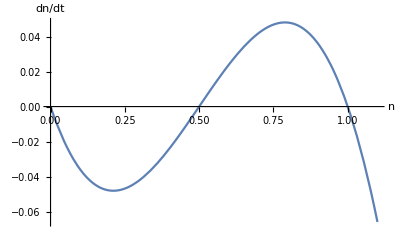

```mathematica
r=1.0;
k=1.0;
a=0.5;

f[n_]:=r*n*(k-n)*(n-a);

Plot[f[n],{n,0,1.1},AxesLabel->{"n","dn/dt"}]
```

### Solve the model numerically for different initial conditions. Can you show multiple stable equilibria?

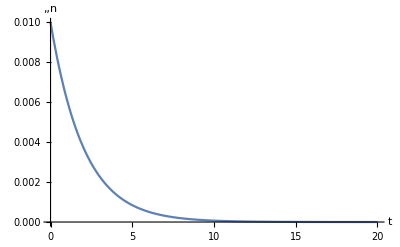

```mathematica
tmax=20;
sol=EcoSim[{n->0.01},tmax];
PlotDynamics[sol]
```

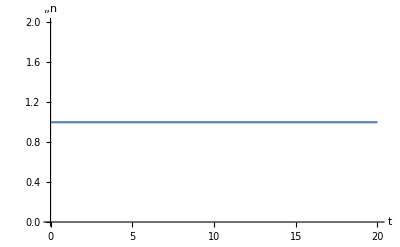

```mathematica
tmax=20;
sol=EcoSim[{n->1},tmax];
PlotDynamics[sol]
```

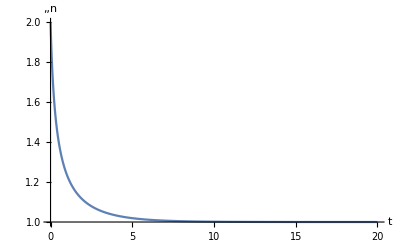

```mathematica
tmax=20;
sol=EcoSim[{n->2},tmax];
PlotDynamics[sol]
```

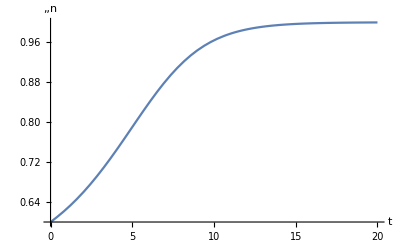

```mathematica
tmax=20;
sol=EcoSim[{n->0.6},tmax];
PlotDynamics[sol]
```

## Discrete-Time Logistic

Here we will explore the discrete logistic equation discussed in class and in May (1974): n[t+1]=n[t]exp[r*(1-n[t]/k)].

```mathematica
SetModel[{Pop[1]->{Variable->n,Equation:>f[n[t]]},ModelType->"DiscreteTime"}];

f[n_]:=n*E^(r*(1-n/k));
```

#### Simulate the difference equation for different values of r (r=0.5,1.2,1.8,2.2,2.6,3.0) What happens?

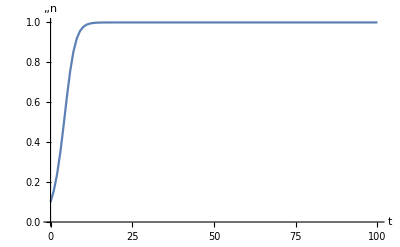

```mathematica
(* set parameters *)
r=0.5;
k=1;

tmax=100;
sol=EcoSim[{n->0.1},tmax];
PlotDynamics[sol]
```

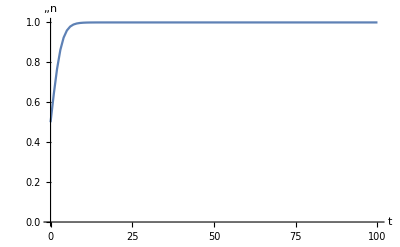

```mathematica
tmax=100;
sol=EcoSim[{n->0.5},tmax];
PlotDynamics[sol]
```

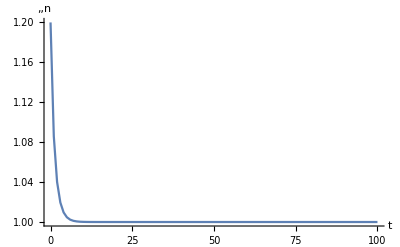

```mathematica
tmax=100;
sol=EcoSim[{n->1.2},tmax];
PlotDynamics[sol]
```

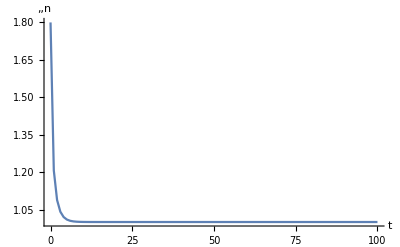

```mathematica
tmax=100;
sol=EcoSim[{n->1.8},tmax];
PlotDynamics[sol]
```

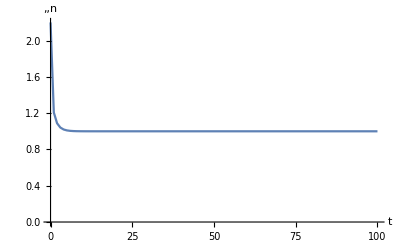

```mathematica
tmax=100;
sol=EcoSim[{n->2.2},tmax];
PlotDynamics[sol]
```

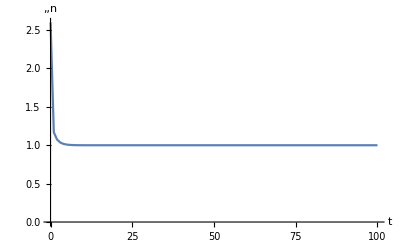

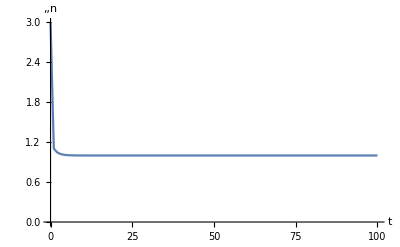

```mathematica
tmax=100;
sol=EcoSim[{n->2.6},tmax];
PlotDynamics[sol]
tmax=100;
sol=EcoSim[{n->3.0},tmax];
PlotDynamics[sol]
```